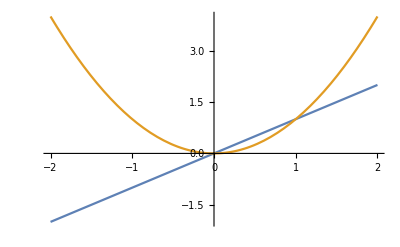

```mathematica
Plot[{x,x x},{x,-2,2}]
```

```mathematica
Plot[{x,x x},{x,-2,2}
,PlotTheme->"Marketing",ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
Plot[{x,x x},{x,-2,2}
,PlotTheme->"Marketing"]
```

-Graphics-

```mathematica
Plot[
{x,x x},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[
{x,x x,Normalize@{x,x}.Normalize@{x,x x}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[
{x,x x,Normalize@{x,D[x,1]}.Normalize@{x,D[x x,2]}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

General::ivar: 1 is not a valid variable.

General::ivar: 2 is not a valid variable.

General::ivar: 1. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[
{x,x x,Normalize@{x,D[x,x]}.Normalize@{x,D[x x,x]}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

General::ivar: -1.99992 is not a valid variable.

General::ivar: -1.91829 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[
{x,x x,Normalize@{x,1}.Normalize@{x,2x}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
FullSimplify[Normalize@{x,D[f[x],x]}.Normalize@{x,D[g[x],x]},x∈Reals]
```

(x^2+f'[x] g'[x])/(√((x^2+Abs[f'[x]]^2) (x^2+Abs[g'[x]]^2)))

```mathematica
FullSimplify[Normalize@{x,D[f[x],x]}.Normalize@{x,D[g[x],x]},{x,f[x],g[x]}∈Reals]
```

(x^2+f'[x] g'[x])/(√((x^2+Abs[f'[x]]^2) (x^2+Abs[g'[x]]^2)))

```mathematica
FullSimplify[Normalize@{x,D[f[x],x]}.Normalize@{x,D[g[x],x]},{x,f[x],g[x],f'[x],g'[x]}∈Reals]
```

(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))

```mathematica
With[{f=Identity,g=Function[x, x x]},
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))
]
```

(2 x+x^2)/(√5 √(x^2 (1+x^2)))

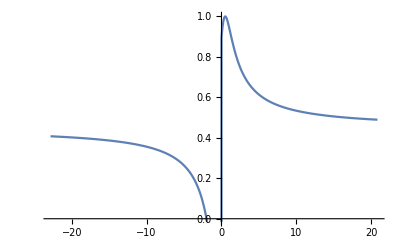

```mathematica
Plot[(2 x+x^2)/(√5 √(x^2 (1+x^2))),{x,-22.84,20.84}]
```

```mathematica
Limit[(2 x+x^2)/(√5 √(x^2 (1+x^2))),x->0]
```

Indeterminate

```mathematica
((2 x+x^2)/(√5 √(x^2 (1+x^2))))/(2x)
```

(2 x+x^2)/(2 √5 x √(x^2 (1+x^2)))

```mathematica
Limit[Integrate[((2 x+x^2)/(√5 √(x^2 (1+x^2))))/a,{x,-a,a}],a->∞]
```

$Aborted

```mathematica
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))
```

```mathematica
Manipulate[Integrate[((2 x+x^2)/(√5 √(x^2 (1+x^2))))/a,{x,-a,a}],{a,1,1000}]
```

```mathematica
Limit[NIntegrate[((2 x+x^2)/(√5 √(x^2 (1+x^2))))/a,{x,-a,a}],a->∞]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

lim_(a→∞) NIntegrate[(2 x+x^2)/((√5 √(x^2 (1+x^2))) a),{x,-a,a}]

```mathematica
FullSimplify[
With[{f=Identity},
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))==Normalize@{x,1}.Normalize@{x,g'[x]}
],{x,f[x],f'[x],g[x],g'[x]}∈Reals]
```

True

```mathematica
With[{f=Identity},
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))==Normalize@{x,1}.Normalize@{x,g'[x]}
]
```

(x^2+g'[x])/(√((1+x^2) (x^2+g'[x]^2)))==x^2/(√(1+Abs[x]^2) √(Abs[x]^2+Abs[g'[x]]^2))+g'[x]/(√(1+Abs[x]^2) √(Abs[x]^2+Abs[g'[x]]^2))

```mathematica
FullSimplify[
With[{f=Identity},
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))==Normalize@{x,1}.Normalize@{x,g'[x]}
],{x,f[x],f'[x]}∈Reals]
```

(x^2+g'[x]) (-1/(√((1+x^2) (x^2+Abs[g'[x]]^2)))+1/(√((1+x^2) (x^2+g'[x]^2))))==0

```mathematica
FullSimplify[
With[{f=Identity},
(x^2+f'[x] g'[x])/(√((x^2+f'[x]^2) (x^2+g'[x]^2)))==Normalize@{x,1}.Normalize@{x,g'[x]}
],{x}∈Reals]
```

(x^2+g'[x]) (-1/(√((1+x^2) (x^2+Abs[g'[x]]^2)))+1/(√((1+x^2) (x^2+g'[x]^2))))==0

```mathematica
DSolve[(x^2+g'[x]) (-1/(√((1+x^2) (x^2+Abs[g'[x]]^2)))+1/(√((1+x^2) (x^2+g'[x]^2))))==0,{g[x]},{x}]
```

{{}}

```mathematica
Solve[(x^2+g'[x]) (-1/(√((1+x^2) (x^2+Abs[g'[x]]^2)))+1/(√((1+x^2) (x^2+g'[x]^2))))==0,g'[x]]
```

{{}}

```mathematica
Plot[
{x,x x,Normalize@{x,1}.Normalize@{x,2x}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

```mathematica
ArcCurvature[{x,x x},x]
```

2/((1+4 x^2)^(3/2))

```mathematica
Plot[
{x,x x,2/((1+4 x^2)^(3/2)),Normalize@{x,1}.Normalize@{x,2x}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
ArcCurvature[{x,x^3},x]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

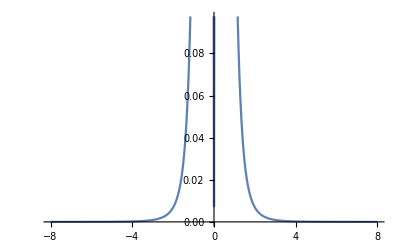

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-8,8}]
```

```mathematica
Plot[
{x,x x,2/((1+4 x^2)^(3/2)),(6 Abs[x])/((1+9 x^4)^(3/2)),Normalize@{x,1}.Normalize@{x,2x}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Normalize@{x,f'[x]}.Normalize@{x,f''[x]}
```

x^2/(√(Abs[x]^2+Abs[f'[x]]^2) √(Abs[x]^2+Abs[f''[x]]^2))+(f'[x] f''[x])/(√(Abs[x]^2+Abs[f'[x]]^2) √(Abs[x]^2+Abs[f''[x]]^2))

```mathematica
FullSimplify[Normalize@{x,f'[x]}.Normalize@{x,f''[x]},{x,f[x],f'[x],f''[x]}∈Reals]
```

(x^2+f'[x] f''[x])/(√((x^2+f'[x]^2) (x^2+f''[x]^2)))

```mathematica
With[{f=Function[x,x x x]},
(x^2+f'[x] f''[x])/(√((x^2+f'[x]^2) (x^2+f''[x]^2)))
]
```

(x^2+18 x^3)/(√37 √(x^2 (x^2+9 x^4)))

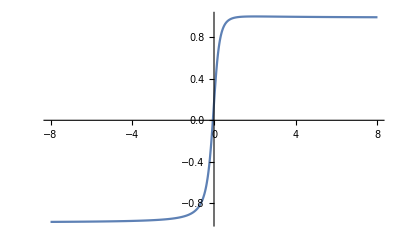

```mathematica
Plot[(x^2+18 x^3)/(√37 √(x^2 (x^2+9 x^4))),{x,-8,8}]
```

```mathematica
Plot[
{x,x x x,(x^2+18 x^3)/(√37 √(x^2 (x^2+9 x^4))),(6 Abs[x])/((1+9 x^4)^(3/2)),Normalize@{x,1}.Normalize@{x,3 x^2}},
{x,-2,2}
,PlotTheme->"Marketing",PlotLegends->"Expressions"]
```

-Graphics-